```mathematica
allGraphs6[6908733,"graph"]
```

-Graphics-

## First the fake graphs

```mathematica
ConnectedComponents[
```

```mathematica
IsFakeGraph[g_,nodes_]:=Block[{comp, pos, sub},
If[VertexCount[g]==nodes,
comp=ConnectedComponents[g];
For[pos=1,pos≤Length[comp],pos++,
sub=Subgraph[g,comp[[pos]]];
If[!CompleteGraphQ[sub], Goto[done]]
];
Return[True]
];
Label[done];
False
]
```

```mathematica
IsGeneratorGraph[allGraphs6[K6Key,"graph"],7]
```

False

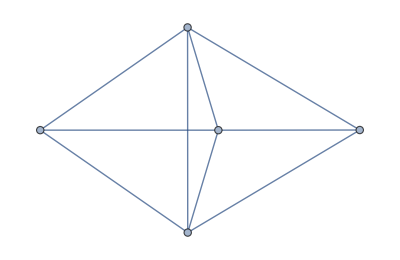
```mathematica
CompleteGraphQ[-Graphics-]
```

False

```mathematica
Table[IsGeneratorGraph[allGraphs5[k,"graph"],5],{k,allGraphs5FakeAtomKeys}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
allGraphs6FakeAtomKeys= Select[Keys[allGraphs6],IsFakeGraph[allGraphs6[#,"graph"],6]&]
```

{0,4782969,7174453,7114644,6995028,6935220,6935221,6636196,6576390,6576393,6456780,6456789,6396975,6396984,6396988,6396978,6396976,5560096,5500341,5500314,5380833,5380752,5320971,5321052,5321080,5320998,5320972,5022325,5022082,4962303,4962546,4962576,4962330,4962306,4842747,4842990,4843080,4842828,4842756,4783212,4783333,4783302,4783242,4783213,4783050,4783078,4783053,4782996,4783005,4782978,4782982,4782972,4782970,1594323,2362324,2303973,2303244,2187273,2185086,2128924,2128194,2126736,2126007,2126008,1837189,1830628,1778844,1778112,1772280,1771551,1771554,1662156,1659960,1655586,1653399,1653408,1600884,1603813,1603080,1601616,1600885,1596510,1597240,1596513,1595052,1595061,1594332,1594336,1594326,1594324,531441,787333,767650,729036,728280,709326,708624,708597,612444,610176,592680,590574,590493,551124,554149,553392,551880,551125,533628,534358,533655,532170,532251,531522,531550,531468,531442,177147,262684,255880,242758,236440,236197,196830,204393,203634,197586,196833,183708,184440,183735,177876,178119,177390,177420,177174,177150,59049,78732,87813,85536,81000,78741,65610,67806,65691,61236,61479,59292,59382,59130,59058,19683,29524,28764,27246,26487,26488,22708,21951,21954,20439,20448,19692,19696,19686,19684,6561,9490,8784,8757,7374,7293,6642,6670,6588,6562,2187,3160,2917,2430,2460,2214,2190,729,972,1062,810,738,243,364,333,273,244,81,109,84,27,36,9,13,3,1}

```mathematica
Length[allGraphs6FakeAtomKeys]
```

203

```mathematica
Table[allGraphs6[k,"graph"],{k,allGraphs6FakeAtomKeys}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Monitor[
Table[
With[
{sets=ConnectedComponents[ allGraphs6[k,"graph"]]},
allGraphs6[k,"colofournull"]=PartitionToSymbol[sets,"p"]
],
{k,allGraphs6FakeAtomKeys}
],k]
```

{p1x2x3x4x5x6,p12x3x4x5x6,p123456,p12345x6,p12346x5,p1234x5x6,p1234x56,p12356x4,p1235x4x6,p1235x46,p1236x4x5,p1236x45,p123x4x5x6,p123x45x6,p123x456,p123x46x5,p123x4x56,p12456x3,p1245x36,p1245x3x6,p1246x35,p1246x3x5,p124x3x5x6,p124x35x6,p124x356,p124x36x5,p124x3x56,p1256x34,p1256x3x4,p125x3x4x6,p125x34x6,p125x346,p125x36x4,p125x3x46,p126x3x4x5,p126x34x5,p126x345,p126x35x4,p126x3x45,p12x34x5x6,p12x3456,p12x345x6,p12x346x5,p12x34x56,p12x35x4x6,p12x356x4,p12x35x46,p12x36x4x5,p12x36x45,p12x3x45x6,p12x3x456,p12x3x46x5,p12x3x4x56,p13x2x4x5x6,p13456x2,p1345x26,p1345x2x6,p1346x25,p1346x2x5,p134x256,p134x25x6,p134x26x5,p134x2x5x6,p134x2x56,p1356x24,p1356x2x4,p135x246,p135x24x6,p135x26x4,p135x2x4x6,p135x2x46,p136x245,p136x24x5,p136x25x4,p136x2x4x5,p136x2x45,p13x24x5x6,p13x2456,p13x245x6,p13x246x5,p13x24x56,p13x25x4x6,p13x256x4,p13x25x46,p13x26x4x5,p13x26x45,p13x2x45x6,p13x2x456,p13x2x46x5,p13x2x4x56,p14x2x3x5x6,p1456x23,p1456x2x3,p145x236,p145x23x6,p145x26x3,p145x2x36,p145x2x3x6,p146x235,p146x23x5,p146x25x3,p146x2x35,p146x2x3x5,p14x23x5x6,p14x2356,p14x235x6,p14x236x5,p14x23x56,p14x25x3x6,p14x256x3,p14x25x36,p14x26x3x5,p14x26x35,p14x2x35x6,p14x2x356,p14x2x36x5,p14x2x3x56,p15x2x3x4x6,p156x234,p156x23x4,p156x24x3,p156x2x34,p156x2x3x4,p15x23x4x6,p15x2346,p15x234x6,p15x236x4,p15x23x46,p15x24x3x6,p15x246x3,p15x24x36,p15x26x3x4,p15x26x34,p15x2x34x6,p15x2x346,p15x2x36x4,p15x2x3x46,p16x2x3x4x5,p16x23x4x5,p16x2345,p16x234x5,p16x235x4,p16x23x45,p16x24x3x5,p16x245x3,p16x24x35,p16x25x3x4,p16x25x34,p16x2x34x5,p16x2x345,p16x2x35x4,p16x2x3x45,p1x23x4x5x6,p1x23456,p1x2345x6,p1x2346x5,p1x234x5x6,p1x234x56,p1x2356x4,p1x235x4x6,p1x235x46,p1x236x4x5,p1x236x45,p1x23x45x6,p1x23x456,p1x23x46x5,p1x23x4x56,p1x24x3x5x6,p1x2456x3,p1x245x36,p1x245x3x6,p1x246x35,p1x246x3x5,p1x24x35x6,p1x24x356,p1x24x36x5,p1x24x3x56,p1x25x3x4x6,p1x256x34,p1x256x3x4,p1x25x34x6,p1x25x346,p1x25x36x4,p1x25x3x46,p1x26x3x4x5,p1x26x34x5,p1x26x345,p1x26x35x4,p1x26x3x45,p1x2x34x5x6,p1x2x3456,p1x2x345x6,p1x2x346x5,p1x2x34x56,p1x2x35x4x6,p1x2x356x4,p1x2x35x46,p1x2x36x4x5,p1x2x36x45,p1x2x3x45x6,p1x2x3x456,p1x2x3x46x5,p1x2x3x4x56}

```mathematica
repFull6=Monitor[ToRules[Reduce[Table[
allGraphs6[k,"colofournull"]==allGraphs6[k,"colofour"],
{k,allGraphs6FakeAtomKeys}
],Table[allGraphs6[k,"colofour"],
{k,allGraphs6AtomKeys}]
]],k]
```

{v1x2x3x4x5x6→p123456,201,v123456→-p123456/120+p12345x6/120+p12346x5/120+p1234x56/120-p1234x5x6/60+p12356x4/120+p1235x46/120-p1235x4x6/60+p1236x45/120-p1236x4x5/60+p123x456/120-p123x45x6/60-p123x46x5/60-p123x4x56/60+p123x4x5x6/20+p12456x3/120+p1245x36/120-p1245x3x6/60+p1246x35/120-p1246x3x5/60+p124x356/120-p124x35x6/60-p124x36x5/60-p124x3x56/60+p124x3x5x6/20+p1256x34/120-p1256x3x4/60+232+p1x256x3x4/20-p1x25x346/60+p1x25x34x6/20+p1x25x36x4/20+p1x25x3x46/20-p1x25x3x4x6/5-p1x26x345/60+p1x26x34x5/20+p1x26x35x4/20+p1x26x3x45/20-p1x26x3x4x5/5-p1x2x3456/60+p1x2x345x6/20+p1x2x346x5/20+p1x2x34x56/20-p1x2x34x5x6/5+p1x2x356x4/20+p1x2x35x46/20-p1x2x35x4x6/5+p1x2x36x45/20-p1x2x36x4x5/5+p1x2x3x456/20-p1x2x3x45x6/5-p1x2x3x46x5/5-p1x2x3x4x56/5+p1x2x3x4x5x6}
 |  |  |  |

```mathematica
repFull6=Map[#[[1]]->Simplify[#[[2]]]&,repFull6]
```

```mathematica
done=0;Monitor[
Table[
done++;
allGraphs6[k,"colofournull"]=(allGraphs6[k,"colofour"]/.repFull6),
{k,Sort[Keys[allGraphs6]]}
],done];
```

```mathematica
Sort[Tally[Table[LeafCount[allGraphs6[k,"colofournull"]],{k,Keys[allGraphs6]}]]]
```

{{1,1},{539,20},{552,1},{555,30},{563,45},{583,60},{609,31},{611,15},{613,15},{1095,60},{1119,90},{1123,60},{1147,180},{1151,60},{1162,31},{1165,90},{1175,90},{1193,180},{1224,60},{1650,60},{1678,120},{1690,90},{1702,360},{1706,60},{1714,180},{1730,180},{1738,180},{1774,90},{1787,45},{1802,180},{1835,60},{2205,20},{2229,60},{2261,60},{2277,180},{2283,45},{2285,180},{2287,60},{2293,45},{2297,180},{2301,60},{2339,90},{2374,20},{2398,180},{2446,30},{2768,15},{2808,90},{2836,360},{2840,60},{2842,180},{2856,180},{2860,360},{2866,180},{2870,120},{2884,60},{2894,360},{2898,20},{2922,180},{2935,30},{2961,180},{2963,60},{3057,6},{3415,180},{3419,90},{3443,180},{3548,180},{3572,405},{3930,180},{3954,360},{3958,180},{3974,45},{3978,360},{3982,360},{4002,180},{4006,420},{4034,180},{4058,270},{4062,60},{4079,15},{4086,360},{4114,45},{4135,420},{4537,180},{4561,360},{4565,360},{4698,90},{4722,180},{4746,120},{5052,90},{5100,180},{5124,180},{5253,180},{5257,60},{5261,90},{5285,360},{5309,450},{5631,180},{5655,180},{5659,360},{5679,180},{5683,540},{5687,180},{5701,90},{5703,90},{5707,360},{5711,180},{5781,60},{5807,60},{5835,60},{5859,180},{5872,432},{5887,90},{5896,60},{6266,180},{6427,360},{6431,360},{6823,180},{6847,360},{6899,180},{6903,180},{6990,360},{6998,360},{7022,360},{7046,240},{7336,180},{7360,180},{7384,450},{7408,180},{7416,60},{7545,45},{7549,180},{7609,180},{8068,15},{8140,180},{8144,360},{8164,360},{8168,360},{8524,420},{8548,180},{8552,360},{8576,180},{8580,180},{8596,15},{8600,180},{8604,360},{8723,360},{8727,450},{8735,180},{8769,20},{8821,45},{9109,45},{9185,180},{9274,60},{9282,360},{9286,720},{9298,180},{9314,180},{9346,120},{9620,60},{9668,90},{9845,60},{10432,360},{10951,120},{10963,90},{10999,720},{11003,360},{11019,270},{11023,720},{11027,360},{11393,180},{11417,360},{11421,60},{11445,360},{11469,360},{11473,180},{11493,60},{11497,90},{11574,120},{11582,180},{11646,15},{12137,180},{12141,360},{12145,180},{12169,720},{12700,360},{12724,180},{12728,360},{13287,360},{13834,60},{13846,360},{13858,360},{13920,10},{14413,15},{14952,180},{14956,180},{14976,180},{14992,90},{15000,540},{15004,720},{15008,90},{15024,360},{15028,360},{15450,45},{15478,180},{15502,180},{15530,180},{15554,90},{16142,540},{16212,90},{16663,15},{16701,720},{16705,720},{16729,540},{17847,180},{18957,360},{18965,10},{18981,450},{19029,90},{19067,180},{19546,120},{19626,180},{20638,60},{20658,360},{20678,180},{20702,360},{20706,720},{20710,480},{21265,360},{21336,90},{21388,60},{22407,360},{23040,60},{23547,180},{23551,180},{23603,360},{23627,360},{24080,90},{25326,60},{26340,180},{26364,360},{26380,60},{26388,360},{26412,180},{28672,72},{29161,6},{29233,120},{29253,360},{29257,90},{29305,360},{29309,360},{30156,15},{30449,360},{30525,45},{33747,180},{33795,60},{37756,30},{37828,60},{37832,360},{37852,90},{37856,360},{37908,180},{39633,45},{43414,20},{49248,60},{49300,180},{49324,180},{49404,15},{64801,60},{64853,45},{86188,15},{116343,1}}

```mathematica
203^2
```

```mathematica
Length[allGraphs6]
```

53071

```mathematica
done=0;Monitor[
Table[
done++;
allGraphs6[k,"colofournull"]=Simplify[allGraphs6[k,"colofournull"]],
{k,Sort[Keys[allGraphs6]]}
],{done,N[done/53071*100,4]}];
```

```mathematica
Sort[Tally[Table[LeafCount[allGraphs6[k,"colofournull"]],{k,Keys[allGraphs6]}]]]
```

```mathematica
Put[allGraphs6,"d:\\saved\\allGraphs6-fullfull.m"]
```

```mathematica
Keys[allGraphs6[0]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofourrealnull,colofournull}

```mathematica
allGraphs6[alfa1Key,"colortable"]//TableForm
```

v124x35x6 | v135x24x6+v16x24x35+v1x24x35x6
v135x24x6 | v124x35x6+v16x24x35+v1x24x35x6
v124x35x6 | v135x24x6+v16x24x35+v1x24x35x6
v135x24x6 | v124x35x6+v16x24x35+v1x24x35x6
v16x24x35 | v124x35x6+v135x24x6+v1x24x35x6
0 | v124x35x6+v135x24x6+v16x24x35+v1x24x35x6
v124x35x6+v135x24x6+v16x24x35+v1x24x35x6 | 0
0 | v124x35x6+v135x24x6+v16x24x35+v1x24x35x6
0 | v124x35x6+v135x24x6+v16x24x35+v1x24x35x6
0 | v124x35x6+v135x24x6+v16x24x35+v1x24x35x6
v124x35x6+v135x24x6+v16x24x35+v1x24x35x6 | 0
0 | v124x35x6+v135x24x6+v16x24x35+v1x24x35x6
0 | v124x35x6+v135x24x6+v16x24x35+v1x24x35x6
0 | v124x35x6+v135x24x6+v16x24x35+v1x24x35x6
0 | v124x35x6+v135x24x6+v16x24x35+v1x24x35x6

## Now the generator graphs

```mathematica
IsGeneratorGraph[g_,nodes_]:=IsFakeGraph[GraphComplement[g],nodes]
```

```mathematica
allGraphs6GeneratorAtomKeys= Select[Keys[allGraphs6],IsGeneratorGraph[allGraphs6[#,"graph"],6]&]
```

{0,7144929,7174089,7174440,7174452,7174453,7174450,7174444,7174426,7174417,7174372,7174369,7174344,7174209,7174210,7174180,7174120,7173724,7173715,7173643,7173481,7173391,7172266,7172263,7172239,7172023,7171993,7171536,7171293,7167891,7167892,7167865,7167811,7167783,7167160,7167079,7165696,7165669,7164963,7154757,7154769,7154770,7154767,7154761,7154014,7154005,7152502,7152499,7151745,7147965,7147966,7147207,7145689,7115404,7115395,7115323,7115161,7115071,7113217,7112974,7108843,7108762,7106647,7095721,7095712,7093453,7088917,7086640,6997306,6997303,6997279,6997063,6997033,6996577,6996334,6990745,6990718,6990013,6977623,6977620,6976867,6970819,6970060,6938256,6938013,6931695,6918573,6911769,6643011,6643012,6642985,6642931,6642903,6642283,6642202,6640825,6640798,6640095,6623328,6623329,6622573,6621061,6620304,6583960,6583879,6581773,6564277,6562009,6465856,6465829,6465127,6446173,6445417,6406803,6387120,5580117,5580129,5580130,5580127,5580121,5579401,5579392,5577943,5577940,5577213,5573568,5573569,5572837,5571373,5570640,5521054,5521045,5518867,5514493,5512297,5402902,5402899,5402173,5396341,5395609,5343825,5337264,5048445,5048446,5047717,5046259,5045529,4989367,4987180,4871209,4870480,4812129,2391120,2391471,2391483,2391484,2391481,2391475,2391457,2391448,2391403,2391400,2391375,2391240,2391241,2391211,2391151,2331706,2331697,2331625,2331463,2331373,2212150,2212147,2212123,2211907,2211877,2152371,2152128,1853481,1853482,1853455,1853401,1853373,1793701,1793620,1674139,1674112,1614357,777465,777477,777478,777475,777469,717673,717664,598063,598060,538257,239232,239233,179425,59809}

```mathematica
Length[allGraphs6GeneratorAtomKeys]
```

203

```mathematica
Table[allGraphs6[k,"graph"],{k,allGraphs6GeneratorAtomKeys}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Monitor[
Table[
With[
{sets=ConnectedComponents[ GraphComplement[allGraphs6[k,"graph"]]]},
allGraphs6[k,"colofourgenerator"]=PartitionToSymbol[sets,"g"]
],
{k,allGraphs6GeneratorAtomKeys}
],k];
```

```mathematica
repFullGen6=Monitor[ToRules[Reduce[Table[
allGraphs6[k,"colofourgenerator"]==allGraphs6[k,"colofour"],
{k,allGraphs6GeneratorAtomKeys}
],Table[allGraphs6[k,"colofour"],
{k,allGraphs6AtomKeys}]
]],k];
```

```mathematica
LeafCount[repFullGen6]
```

6686

```mathematica
repFullGen6=Map[#[[1]]->Simplify[#[[2]]]&,repFullGen6];
```

```mathematica
LeafCount[repFullGen6]
```

6686

```mathematica
done=0;Monitor[
Table[
done++;
allGraphs6[k,"colofourgenerator"]=(allGraphs6[k,"colofour"]/.repFullGen6),
{k,Sort[Keys[allGraphs6]]}
],done];
```

```mathematica
done=0;Monitor[
Table[
done++;
allGraphs6[k,"colofourgenerator"]=Simplify[allGraphs6[k,"colofourgenerator"]],
{k,Sort[Keys[allGraphs6]]}
],{done,N[done/53071*100,4]}];
```

```mathematica
Put[allGraphs6,"d:\\saved\\allGraphs6-fullfullgen.m"]
```